```mathematica
a*Cos[omega1*t]+a*Cos[omega2*t]
```

a Cos[omega1 t]+a Cos[omega2 t]

```mathematica
a (2 Cos[(omega1 t)/2-(omega2 t)/2] Cos[(omega1 t)/2+(omega2 t)/2])
```

a (Cos[omega1 t]+Cos[omega2 t])

```mathematica
Solve[-1/Abs[x+2]+1/Abs[x-2]==1/2,{x},Reals]
```

{{x→2 √3},{x→2 (-1+√2)}}

```mathematica
Solve[-1/Abs[1+2]+1/Abs[1-2]==v,{v},Reals]
```

{{v→2/3}}

```mathematica
r1 = √((x-x1)^2+(y-y1)^2)
r2 = √((x-x2)^2+(y-y2)^2)
q1/r1+q2/r2
```

√((x-x1)^2+(y-y1)^2)

√((x-x2)^2+(y-y2)^2)

q1/(√((x-x1)^2+(y-y1)^2))+q2/(√((x-x2)^2+(y-y2)^2))

```mathematica
D[(q1/(√((x-x1)^2+(y-y1)^2))+q2/(√((x-x2)^2+(y-y2)^2))), y]
```

-(q1 (y-y1))/(((x-x1)^2+(y-y1)^2)^(3/2))-(q2 (y-y2))/(((x-x2)^2+(y-y2)^2)^(3/2))

```mathematica
Simplify[-(q1 (y-y1))/(((x-x1)^2+(y-y1)^2)^(3/2))-(q2 (y-y2))/(((x-x2)^2+(y-y2)^2)^(3/2))]
```

(q1 (-y+y1))/(((x-x1)^2+(y-y1)^2)^(3/2))+(q2 (-y+y2))/(((x-x2)^2+(y-y2)^2)^(3/2))

```mathematica
D[(q1/(√((x-x1)^2+(y-y1)^2))+q2/(√((x-x2)^2+(y-y2)^2))), x]
```

-(q1 (x-x1))/(((x-x1)^2+(y-y1)^2)^(3/2))-(q2 (x-x2))/(((x-x2)^2+(y-y2)^2)^(3/2))

```mathematica
Simplify[-(q1 (x-x1))/(((x-x1)^2+(y-y1)^2)^(3/2))-(q2 (x-x2))/(((x-x2)^2+(y-y2)^2)^(3/2))]
```

(q1 (-x+x1))/(((x-x1)^2+(y-y1)^2)^(3/2))+(q2 (-x+x2))/(((x-x2)^2+(y-y2)^2)^(3/2))

```mathematica
(q1 (-y+y1))/(((x-x1)^2+(y-y1)^2)^(3/2))+(q2 (-y+y2))/(((x-x2)^2+(y-y2)^2)^(3/2))/.{x1-> -2,y1-> 0,x2-> 2,y2-> 0,q1-> -1,q2-> 1}
```

```mathematica
-y/(((-2+x)^2+y^2)^(3/2))+y/(((2+x)^2+y^2)^(3/2))
```

-y/(((-2+x)^2+y^2)^(3/2))+y/(((2+x)^2+y^2)^(3/2))

```mathematica
-y/(((-2+x)^2+y^2)^(3/2))+y/(((2+x)^2+y^2)^(3/2))/.{x-> 2 (-1+√2),y-> 0.}
N[-(q1 (x-x1))/(((x-x1)^2+(y-y1)^2)^(3/2))-(q2 (x-x2))/(((x-x2)^2+(y-y2)^2)^(3/2))/.{x1->-2,x2-> 2,y1-> 0,y2-> 0,x->2 (-1+√2) ,y-> 0,q1-> -1,q2-> 1}]
```

0.

```mathematica
0.853553390593274*10^-3
```

0.000853553

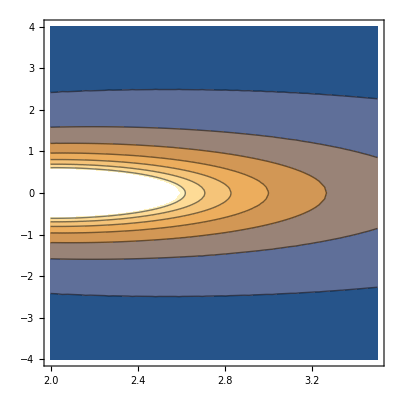

```mathematica
ContourPlot[1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2)),{x,2,3.5},{y,-4,4}]
```

```mathematica
q1/(√((x-x1)^2+(y-y1)^2))+q2/(√((x-x2)^2+(y-y2)^2))/.{x1->-2,x2-> 2,y1-> 0,y2-> 0,q1-> -1,q2-> 1}
```

1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2))

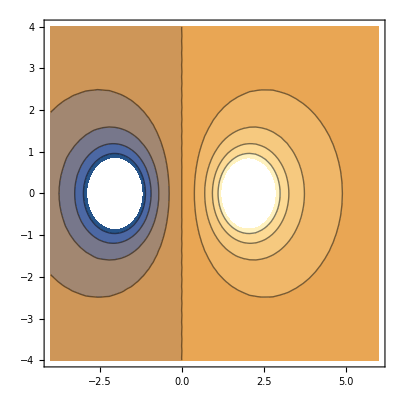

```mathematica
ContourPlot[1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2)),{x,-4,6},{y,-4,4}]
```

```mathematica
1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2))/.y-> 0
```

```mathematica
1/(√((-2+x)^2))-1/(√((2+x)^2))==0.25
```

1/(√((-2+x)^2))-1/(√((2+x)^2))==0.25

```mathematica
Solve[1/(√((-2+x)^2))-1/(√((2+x)^2))==0.25,{x},Reals]
```

{{x→0.472136},{x→4.47214}}

```mathematica
1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2))-0.25
```

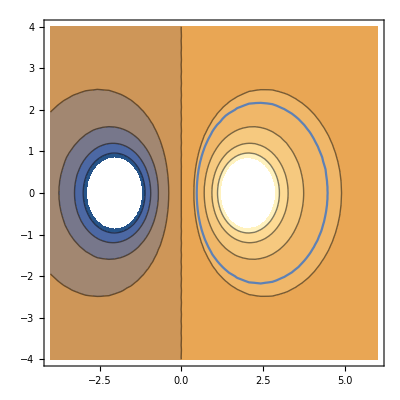

```mathematica
Show[
{
ContourPlot[1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2)),{x,-4,6},{y,-4,4}],
ContourPlot[1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2))==0.25,{x,-4,6},{y,-4,4}]
}]
```